```mathematica
(* ========================================= *)
```

```mathematica
NotebookEvaluate["/home/essam/EAD/Notebooks/SetParameters.nb"];
```

```mathematica
NotebookEvaluate["/home/essam/EAD/Notebooks/Preprocessing.nb"];
```

```mathematica
(*NetworkName=Region1<>"_"<>ToString[t];*)
```

```mathematica
(*TrainingData=Table[makeRule3[InputTrain[[i;;i+Days-1]],OutputTrain[[i+Days]]],{i,1,Dimensions[InputTrain][[1]]-Days}]; *)
```

```mathematica
TrainingData=Table[makeRule3[InputTrain[[i;;i+Days-1]],OutputTrain[[i+Days;;i+Days+Future1-1]]],{i,1,Dimensions[InputTrain][[1]]-Days-Future1-1}];
```

```mathematica
(*ValidationData=Table[makeRule3[InputTest[[i;;i+Days-1]],TrueTest[[i+Days]]],{i,1,Dimensions[InputTest][[1]]-Days}];*)
```

```mathematica
ValidationData=Table[makeRule3[InputTest[[i;;i+Days-1]],TrueTest[[i+Days;;i+Days+Future1-1]]],{i,1,Dimensions[InputTest][[1]]-Days-Future1-1}];
```

```mathematica
testingData=Table[InputTest[[i;;i+Days-1]],{i,1,Dimensions[InputTest][[1]]-Days}];
```

```mathematica
testingTrue=Table[TrueTest[[i+Days]],{i,1,Dimensions[InputTest][[1]]-Days}];
```

```mathematica
NotebookEvaluate["/home/essam/EAD/Notebooks/Arch2.nb"];
```

```mathematica
logFile=CreateTemporary[]; (* save training data into TMP file *)
```

```mathematica
appendToLog=PutAppend[<|"Batch"->#AbsoluteBatch,"Loss"->#RoundLoss,"VLoss"->#ValidationLoss|>,logFile]&;
```

```mathematica
trained=NetTrain[net,TrainingData,BatchSize->BS,MaxTrainingRounds->Epochs,ValidationSet->ValidationData,TargetDevice->{"GPU",All},  TrainingProgressFunction->appendToLog];
```

```mathematica
x=trained[testingData];
```

```mathematica
Dimensions[x]
```

{232,28}

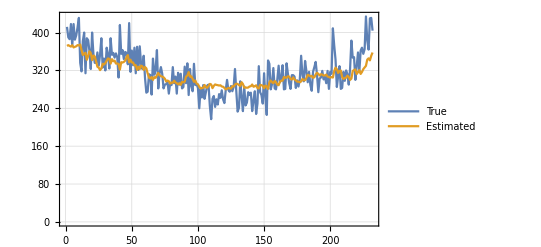

```mathematica
ListLinePlot[{testingTrue,x[[;;,1]]},PlotLegends->{"True","Estimated"},PlotTheme->"Detailed"]
```

```mathematica
(*Export["/home/essam/Prediction_covid_cases/NN3/"<>NetworkName<>".wlnet",trained];*)
```

```mathematica
Export["/home/essam/EAD/Results/28days.xls",x];
```